```mathematica
H = Table[RandomReal[{0.1,1}],4];
μ = Table[RandomReal[{0.01,0.1}],4];
δ = Table[RandomReal[{0.01,0.1}],3];
S = Table[RandomReal[5],4];
ciC = Table[RandomReal[5],4];
ciX = Table[RandomReal[5],3];
```

```mathematica
V = {
	{0,RandomReal[1],RandomReal[1]},
	{0,0,RandomReal[1]},
	{0,0,RandomReal[1]},
	{0,0,RandomReal[1]}
	};
W = {
	{RandomReal[1],0,0},
	{RandomReal[1],0,0},
	{0,RandomReal[1],0},
	{0,RandomReal[1],0}
};
```

```mathematica
V//MatrixForm;
```

(0 | 0.380761 | 0.402629
0 | 0 | 0.468129
0 | 0 | 0.7224
0 | 0 | 0.016485)

```mathematica
W//MatrixForm;
```

(0.25464 | 0 | 0
0.516674 | 0 | 0
0 | 0.613466 | 0
0 | 0.260879 | 0)

```mathematica
concentrationsGen[N_]:=
	Module[{X,i},
		X[t_] = {};
		For[i=1,i≤ N,i++,
			X[t_] = AppendTo[X[t],ToExpression["c"<>ToString[i[t]]]]
		];
	Return[X[t]]
	]
```

```mathematica
speciesGen[N_]:=
	Module[{X,i},
		X[t_] = {};
		For[i=1,i≤ N,i++,
			X[t_] = AppendTo[X[t],ToExpression["x"<>ToString[i[t]]]]
		];
	Return[X[t]]
	]
```

```mathematica
G[c_, v_] := v.c
```

```mathematica
R[i_]:= (c[t]⟦i⟧)/(H⟦i⟧+c[t]⟦i⟧)
```

```mathematica
c[t_]=concentrationsGen[4];
x[t_] = speciesGen[3];
```

```mathematica
vars[t_]=Flatten[{c[t],x[t]}];
```

```mathematica
g1 = G[V⟦;;,1⟧,c[t]];
g2 = G[V⟦;;,2⟧,c[t]];
g3 = G[V⟦;;,3⟧,c[t]];
g = {g1,g2,g3};
```

```mathematica
r = Table[R[i],{i,1,4}];
```

```mathematica
eqC = Table[c'[t]⟦i⟧==S⟦i⟧ +( W.x[t])⟦i⟧ r⟦i⟧-(V.x[t])⟦i⟧r⟦i⟧-(μ⟦i⟧c[t]⟦i⟧),{i,1,Length[c[t]]}];
eqX = Table[x'[t]⟦i⟧==x[t]⟦i⟧(g⟦i⟧-δ⟦i⟧),{i,1,Length[x[t]]}];
cisC = Table[c[0]⟦i⟧==ciC⟦i⟧,{i,1,Length[c[t]]}];
cisX = Table[x[0]⟦i⟧==ciX⟦i⟧,{i,1,Length[x[t]]}];
```

```mathematica
sistema = Flatten[{eqC,eqX,cisX,cisC}];
```

```mathematica
sol=NDSolve[sistema,vars[t],{t,0,100}];
```

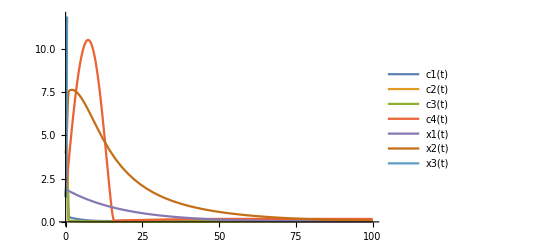

```mathematica
Plot[Evaluate[vars[t]/.sol],{t,0,100},PlotLegends->vars[t]]
```